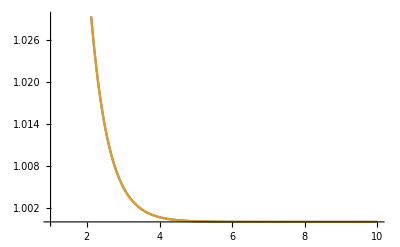

```mathematica
Plot[{Coth[w],1/Tanh[w]},{w,1,10}]
```

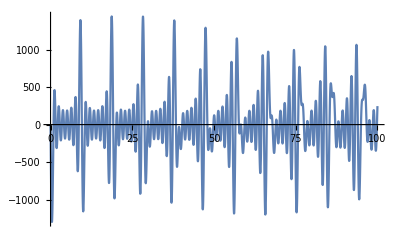

```mathematica
wList={0.6418859884798135,1.2894916071279168,1.9429944981523035,2.602562164189078,3.2683533388636996,3.9405185996989096,4.6192011408588645,5.304537809885728,5.996660350639525,6.695696756121709,7.401772639057949,8.115012548244128,8.835541182667484,9.563484477404593,10.298970552725388,11.042130530219238,11.793099227519507,12.552015747365125,13.319023978246552,14.094273023679984,14.877917575915871,15.670118248142439,16.47104187733661,17.28086180804969,18.099758165717823,18.927918126612138,19.765536190306364,20.612814459527346,21.469962931458383,22.337199803937533,23.214751799537837,24.102854510176304,25.001752764680752,25.911701021605253,26.832963789532435,27.76581607710369,28.71054387508161,29.667444672855726,30.636828011955494,31.619016079324233,32.61434434333804,33.62316223581977,34.64583388360535,35.682738893565194,36.73427319537506,37.800849946768686,38.88290050649447,39.98087548075027,41.09524584948413,42.22650417964023,43.37516593320371,44.54177087876947,45.72688461633981,46.931100226163466,48.155040053677496,49.39935764403091,50.664739841274724,51.95190906913187,53.26162581234204,54.59469131995777,55.95195055469101,57.33429541553852,58.74266826451135,60.17806579244636,61.6415432636786,63.13421918492303,64.65728045019229,66.21198802113503,67.79968321102427,69.42179465100752,71.07984602946298,72.77546470976459,74.51039134891032,76.28649065989943,78.10576348517058,79.970360377747,81.88259692211437,83.8449710697335,85.86018281630575,87.93115661184008,90.06106697328606,92.25336786700268,94.51182654991023,96.84056271084077,99.24409394682368,101.72738885572258,104.29592934470871,106.95578416888381,109.71369626284495,112.5771871654872,115.5546828517452,118.65566671864877,121.89086758615396,125.27249387972391,128.81453081800416,132.53312846910634,136.4471345461187,140.57890499014496,144.95586831274687,149.61595332328773,1384.3902121938977};cList={-6.046989594398401,8.518888051299209,10.359051379730202,-11.841496152719955,-13.0723907437104,-14.107803297312465,-14.983205286559206,-15.723929759257462,16.349609256678892,16.8762809546321,17.317470623217428,17.68479470821588,17.98832404902812,-18.236825669818387,-18.437940026051898,-18.598322268121436,-18.723761674608053,18.819286185618054,18.889255411960768,18.937443817498913,18.96711503674054,18.981088009075695,-18.981795532113885,-18.971335833260554,-18.951517771782523,-18.923900288431533,-18.8898267093601,18.8504544858259,18.80678091462234,18.759665340558403,18.709848295040768,-18.657967977020206,-18.604574436089468,-18.550141773830887,-18.49507863938636,18.43973725878899,18.38442120533108,18.329392089554023,18.274875322485848,-18.221065083944076,-18.16812860892098,-18.11620988877667,18.065432870063923,18.015904221800504,17.967715731777027,17.92094638372104,-17.875664159653155,-17.831927605375785,-17.78978719156623,17.74928649827388,17.7104632466197,17.673350198076736,-17.637975938740468,-17.604365563490603,-17.57254127271622,17.542522892385044,17.514328326545318,17.487973949864998,-17.46347494647432,-17.440845600150126,17.42009953973318,17.40124994256472,-17.38430969762182,-17.369291528906434,-17.35620807841475,17.345071946668394,17.33589568723412,-17.3286917498258,-17.323472364357254,17.320249355551976,-17.3190338742517,-17.31983602712665,17.32266438075202,17.327525308503212,-17.334422138788742,17.343354049881746,-17.354314638710537,17.367290066539937,-17.382256650880127,17.39917772596317,-17.41799952791862,17.438645765821175,-17.461010401905796,17.484947960450057,-17.510260378255175,17.536678938911916,-17.563839093700597,17.59124478049911,-17.618216875301723,17.64381701963655,-17.666732019448208,17.685092725182965,17.69617907507623,-17.69591625711053,17.6779604896854,-17.631904329892393,17.539356281187356,-17.363952814244936,17.018898091865516,-16.19912480931177,-828.2229687682933};
cS[c_,w_,t_,T_]:=(π/2) c^2  (Cos[w*t]/Tanh[w/(2T)]-ⅈ Sin[w*t]);
corr[t_,T_]:=Sum[cS[cList[[n]],wList[[n]],t,T],{n,1,7}];
Plot[Im[corr[t,30]],{t,0,100}]
```

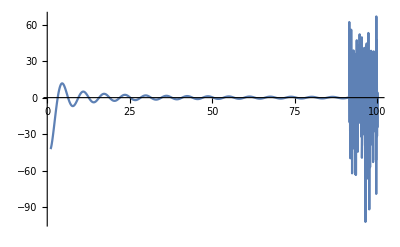

```mathematica
Plot[NIntegrate[(Cos[w*t]/Tanh[w/(2*30)])1*w*ⅇ^(-w/10),{w,1,Infinity}],{t,1,100},PlotRange->All]
```

```mathematica
Integrate[(Cos[w*t]/Tanh[w/(2*30)])1*ⅇ^(w/10),{w,1,10000}]/.{t->10}
```

1/10 (ⅈ ⅇ^(-10 ⅈ) Hypergeometric2F1[-300 ⅈ,1,1-300 ⅈ,ⅇ^(1/30)]+ⅈ ⅇ^(-100000 ⅈ) (-Hypergeometric2F1[-300 ⅈ,1,1-300 ⅈ,ⅇ^(1000/3)]+ⅇ^(200000 ⅈ) Hypergeometric2F1[300 ⅈ,1,1+300 ⅈ,ⅇ^(1000/3)])+1/20253150122501(-100 (1350195006+2700300003 ⅇ^(1/30)+2025112501 ⅇ^(1/15)) ⅇ^(1/30) Cos[10]-20253150122501 ⅈ ⅇ^(10 ⅈ) Hypergeometric2F1[300 ⅈ,1,1+300 ⅈ,ⅇ^(1/30)]-2 (1+10125000000000 (2+2 ⅇ^(1/30)+2 ⅇ^(1/15)+ⅇ^(1/10))+2500 (49+36 ⅇ^(1/30)+9 ⅇ^(1/15)+2 ⅇ^(1/10))+112500000 (28+26 ⅇ^(1/30)+20 ⅇ^(1/15)+5 ⅇ^(1/10))) Sin[10])+1/20253150122501 2 (5 (13501950060 ⅇ^(1000/3)+27003000030 ⅇ^(2000/3)+20251125010 ⅇ^1000) Cos[100000]+(1+10125000000000 (2+2 ⅇ^(1000/3)+2 ⅇ^(2000/3)+ⅇ^1000)+2500 (49+36 ⅇ^(1000/3)+9 ⅇ^(2000/3)+2 ⅇ^1000)+112500000 (28+26 ⅇ^(1000/3)+20 ⅇ^(2000/3)+5 ⅇ^1000)) Sin[100000]))